# South Side... Myth?

Mark Greenberg

## Background

Six years ago, when I was teaching at Cyber High School in Phoenix, I remarked to my class that the south sides of major cities seemed to have more crime. I grew up listening to Jim Croce’s song Bad, Bad Leroy Brown which begins “The south side of Chicago is the baddest part of town,” hearing my dad tell stories of rough and tumble South Boston, and other references that linked “south side” with crime. Cyber High was an urban school. The students were from inner-city Phoenix, including Desiré from Phoenix’s south side. She took offense and respectfully told me that the comment was racist. I didn’t think so, so I recommended to her that she investigate the question, do a little research into the crime rates of different neighborhoods in big cities. She never did, but the question stuck in my head.

## First Approach

The Wolfram curated database has entities for every county in the US, each with several crime properties. So having the data should bring me a little closer to what I want to know.

```mathematica
counties=Cases[GeoNearest["AdministrativeDivision",Entity["City",{"LosAngeles","California","UnitedStates"}],{All,Quantity[50,"Miles"]}],Entity[_,{_,_,_}]];
crimeProps=Cases[EntityValue[counties⟦1⟧,"Properties"],EntityProperty[_,a_/;StringContainsQ[a,"Crime"]]];
Column[{counties,crimeProps}]
```

{Ventura County, California, United States,Los Angeles County, California, United States,Orange County, California, United States,Riverside County, California, United States,Kern County, California, United States,San Diego County, California, United States}
{total rate of crime,total number of crimes,total rate of property crime,total number of property crimes,total rate of violent crime,total number of violent crimes}

This looks promising, but there are two problems with this approach. First, counties are not a very good division for this, neighborhoods would be better. A more critical problem is this:

```mathematica
EntityValue[counties,crimeProps,"EntityPropertyAssociation"]/.Missing["NotAvailable"]->Style[Missing["NotAvailable"],{Red,Bold}]
```

<|Ventura County, California, United States→<|total rate of crime→Missing[NotAvailable],total number of crimes→Missing[NotAvailable],total rate of property crime→Missing[NotAvailable],total number of property crimes→Missing[NotAvailable],total rate of violent crime→Missing[NotAvailable],total number of violent crimes→Missing[NotAvailable]|>,Los Angeles County, California, United States→<|total rate of crime→Missing[NotAvailable],total number of crimes→Missing[NotAvailable],total rate of property crime→Missing[NotAvailable],total number of property crimes→Missing[NotAvailable],total rate of violent crime→Missing[NotAvailable],total number of violent crimes→Missing[NotAvailable]|>,Orange County, California, United States→<|total rate of crime→Missing[NotAvailable],total number of crimes→Missing[NotAvailable],total rate of property crime→Missing[NotAvailable],total number of property crimes→Missing[NotAvailable],total rate of violent crime→Missing[NotAvailable],total number of violent crimes→Missing[NotAvailable]|>,Riverside County, California, United States→<|total rate of crime→Missing[NotAvailable],total number of crimes→Missing[NotAvailable],total rate of property crime→Missing[NotAvailable],total number of property crimes→Missing[NotAvailable],total rate of violent crime→Missing[NotAvailable],total number of violent crimes→Missing[NotAvailable]|>,Kern County, California, United States→<|total rate of crime→Missing[NotAvailable],total number of crimes→Missing[NotAvailable],total rate of property crime→Missing[NotAvailable],total number of property crimes→Missing[NotAvailable],total rate of violent crime→Missing[NotAvailable],total number of violent crimes→Missing[NotAvailable]|>,San Diego County, California, United States→<|total rate of crime→Missing[NotAvailable],total number of crimes→Missing[NotAvailable],total rate of property crime→Missing[NotAvailable],total number of property crimes→Missing[NotAvailable],total rate of violent crime→Missing[NotAvailable],total number of violent crimes→Missing[NotAvailable]|>|>

## Second Approach

It would be better to have crime statistics for neighborhoods. I was able to find on the Internet a source of neighborhood crime statistics for my home town of Los Angeles, LAtimes.com. The data below shows the rate of violent crime per 10,000 people and the total number of crimes over the most recent 6-month period.

```mathematica
url="http://maps.latimes.com/neighborhoods/violent-crime/neighborhood/list/";
data=Flatten[Import[url,"Data"]⟦2,2,All⟧,{1}];
trimmedData=data⟦;;,2;;3⟧/.s_String->StringTrim[s];
Row[Dataset[data],Dataset[trimmedData]]
```

StringTrim::strse: String or list of strings expected at position 1 in StringTrim[s].

Row[Dataset[<>],Dataset[<>]]

That’s current, detailed information at the resolution I need to answer the question. There are some problems with this avenue though. This data source is for Los Angeles only. Doubtless there are similar sets of data for other big cities, but collecting each separately would be a tedious, inefficient, and spotty way to answer the question. Let’s see though if the idea holds for this one city at least.

```mathematica
hoodsAll=DeleteCases[{Interpreter["Neighborhood"][#⟦1⟧],#⟦2⟧}&/@trimmedData,{_Failure,_}];
hoodsCal=Cases[hoodsAll,{Entity[_,s_/;StringContainsQ[s,"California"]],_}];
hoodsDir=Quiet[Append[#,GeoDirection[#⟦1⟧,Entity["City",{"LosAngeles","California","UnitedStates"}]]]&/@hoodsCal];
magAngle={Cos[#⟦3⟧],#⟦2⟧}&/@hoodsDir
```

{{-0.85195,109.6},{-0.732516,54.3},{-0.444762,32.2},{0.496037,29.6},{-0.0778523,27.5},{-0.98233,26.1},{-0.753351,24.1},{-0.996708,21.7},{0.940913,21.4},{-0.821437,21.3},{0.923304,21.1},{-0.504057,20.6},{-0.994499,20.3},{-0.952923,19.8},{-0.59452,19.7},{-0.418542,18.},{-0.999987,17.8},{-0.894546,17.3},{-0.934482,17.2},{-0.747437,16.9},{0.854968,15.7},{-0.615155,15.5},{-0.343478,14.9},{-0.99084,13.9},{-0.651338,13.8},{-0.997317,13.8},{-0.992244,13.4},{-0.932994,12.3},{-0.515886,12.1},{0.94906,11.5},{-0.98961,11.3},{-0.968773,10.8},{-0.803359,9.9},{-0.854404,9.6},{0.75244,7.9},{-0.931429,6.7},{0.50951,6.4},{-0.936754,5.8},{0.62424,4.8},{-0.633184,4.5},{-0.914695,4.3},{-0.230111,3.5},{-0.92582,3.1},{-0.993302,2.5},{0.106162,2.5},{-0.235739,1.1},{-0.918563,0.}}

My first thought is to create a map because this is geographic data, but a map would not answer the question directly. Plus, the data is too spotty to make an interesting map. Instead, this scatter plot shows the correlation between the vertical component of the angle from the center of Los Angeles to the center of the neighborhood.

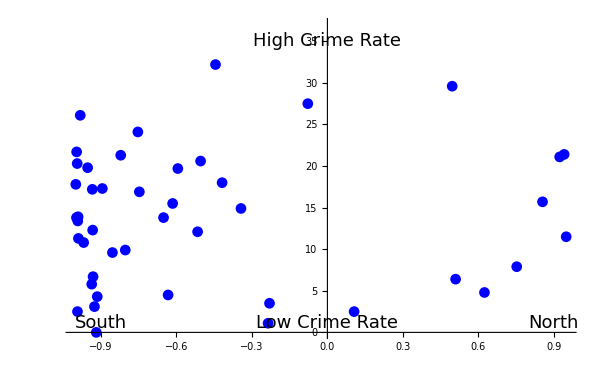

```mathematica
ListPlot[
magAngle,
Epilog->{
Text[Style["South",18],{-.9,1.1}],
Text[Style["North",18],{.9,1.1}],
Text[Style["High Crime Rate",18],{0,35}],
Text[Style["Low Crime Rate",18],{0,1.1}]},
PlotStyle->Blue,PlotRange->37,Ticks->None,AxesStyle->{Thick,Black},ImageSize->600]
```

And finally, the average number of violent crimes per 10,000 people in the most recent six-month period in the southern neighborhoods of Los Angeles vs those in the northern neighborhoods:

```mathematica
south=Cases[magAngle,{a_,_}/;a<0];
north=Complement[magAngle,south];
sMean=Round[Mean[Last/@south],.01];
nMean=Round[Mean[Last/@north],.01];
Style[StringForm["Overall Crime Rate in Southern Neighborhoods: `1`\nOverall Crime Rate in Northern Neighborhoods: `2`",sMean,nMean],{24,FontFamily->"Times New Roman"}]
```

Overall Crime Rate in Southern Neighborhoods: 17.56
Overall Crime Rate in Northern Neighborhoods: 13.43

In this case, the south side neighborhoods are a little higher in crime.

## Conclusion

This analysis doesn’t really answer Desiré’s question. Are cities’ south sides more crime ridden? In Los Angeles, it seems so, at least in those neighborhoods that I could get data for. To answer the question generally, data would have to cover more major cities in the United States. To answer it accurately, we would need to gather crime data on all neighborhoods. The FBI, the official data source for crime data, does not make available neighborhood crime data, so I’m not sure whether it is even obtainable nationwide.

Finally, what about Desiré’s assertion that my statement was racist. I don’t think so, but people can say racist things without being aware of it. We could follow that up with another analysis of the races of the people who live in south side neighborhoods. If south sides are consistently heavier in people of color but not statistically the “baddest part of town,” then maybe Desiré has a point.